```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
CloudGet["https://www.wolframcloud.com/objects/8549bab6-7b14-4b2a-b77a-8944882d6562"]
```

# How to Fix the House of Representatives

Okay, we have everything we need to start a computational experiment on how the House of Representatives--and, by extension, the Electoral College--could be adjusted for better representation without the need for a Constitutional amendment.

The Constitution stipulates that the number of representatives per state should be reapportioned after each decennial census based on state populations. It does not specify the total number of representatives or the exact method of allotment, other than specifying that each state should have at least one representative.

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one seat to each state, leaving 385 remaining. The 50 states are then allocated these remaining seats one-by-one according to which one has the highest priority according to a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

We’re going to start by using this algorithm and adjusting the size and default starting and ending points. Later, we’ll toy around with other algorithms. Each one we consider will take just two arguments: The population of the state and its current number of seats during the iterative process of assigning them, like so:

PriorityHuntingtonHill[stateAbbr_, stateReps_] := 
	1.0 * statesByAbbreviation[stateAbbr][“population_decennial”][“2010”] / 	Sqrt[stateReps * (stateReps + 1)]

## Let’s see if there’s an ideal size of the House

One of the beauties of the Wolfram language is that it lends itself to running computational experiments. Let’s try a bunch of different House sizes, up to twice the current size, and see if there’s an ideal number of representatives for the lowest variance in the representative-per-person ratios from state-to-state. Let’s start by looking at the coefficient of variance between the population of each state divided by the number of seats it holds.

```mathematica
GetVariance[houseSize_] := (
	allocation = CalculateAllocations[houseSize, 1, 0, PriorityHuntingtonHill];
	ratio = PeoplePerRepresentative[allocation];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio
)
```

This will take just a second since we’re running about 700 simulations, all of which require taking a lot of square roots.

```mathematica
houseSizes = Range[150,870];
variances = GetVariance /@ houseSizes;
```

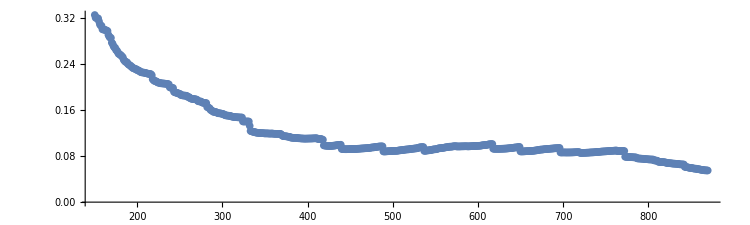

```mathematica
ListPlot[Transpose[{houseSizes, variances}], ImageSize->750, AspectRatio->0.3, PlotRange->Automatic, PlotRange->All]
```

This is curious. We’d certainly expect the variance decline as the House grows larger, but there are certain breaking points where one extra seat significantly reduces the disparity. This won’t fix the Electoral College by itself, but let’s identify those points where there is at least a modest drop.

```mathematica
indices = Select[Most[Range[Length@variances]], variances[[#]] / variances[[# + 1 ]] > 1.05&] + 1;
values = variances[[#]]& /@ indices;
idealSizes = houseSizes[[#]]& /@ indices
```

{332,333,419,440,489,537,618,650,697,773,843}

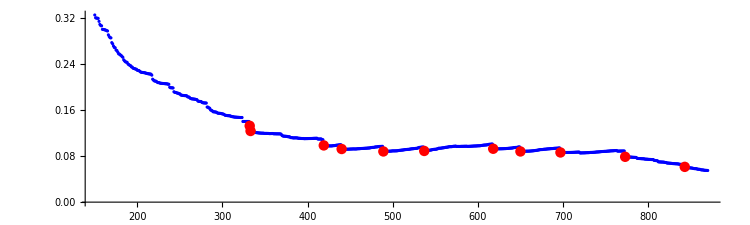

```mathematica
ListPlot[{Transpose[{houseSizes, variances}], Transpose[{idealSizes, values}]},
	ImageSize -> 750, AspectRatio -> 0.3, PlotRange->Full, PlotStyle->{{Blue, PointSize[0.003]},{Red, PointSize[0.01]}}
]
```

Now, out of curiosity, let’s see what the per-representatives ratios looks like at a few of these points compared to the current House.

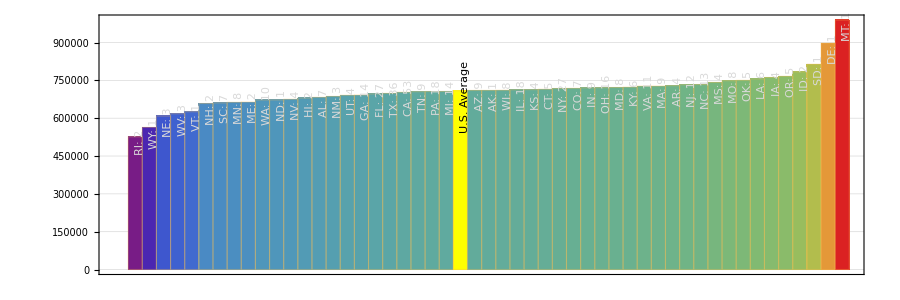
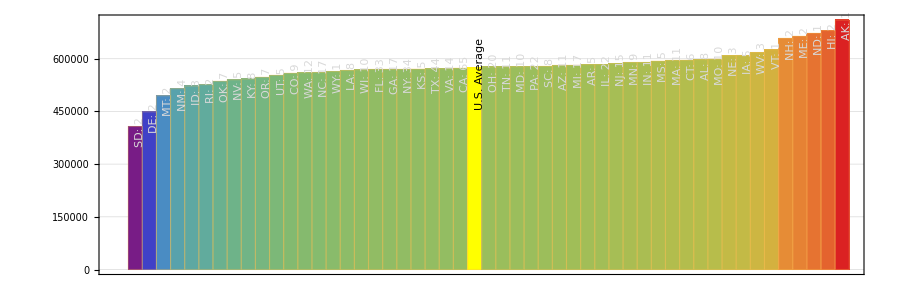
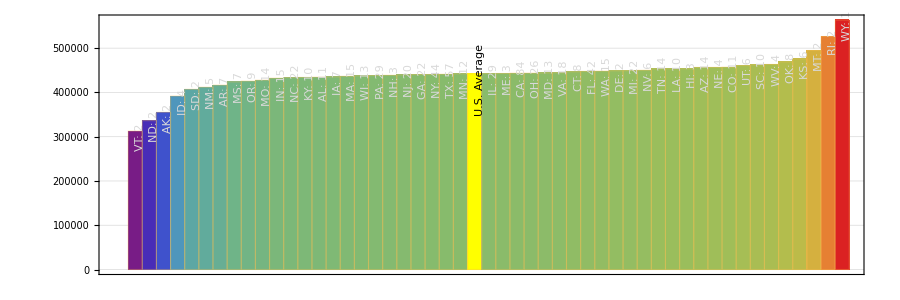
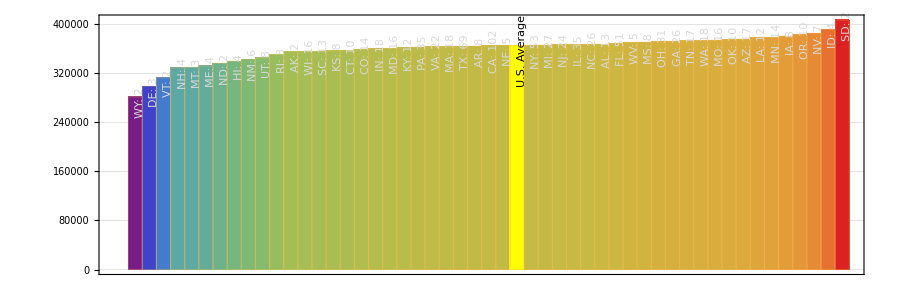
-Graphics-435 Seats | -Graphics-537 Seats | 
-Graphics-697 Seats | -Graphics-843 Seats |

```mathematica
Grid[{
	{
		Labeled[Magnify[VisualizeRepresentation[houseOfRepresentatives], 0.5], Style["435 Seats", FontSize->14], Bottom],
		Labeled[Magnify[VisualizeRepresentation[CalculateAllocations[537]], 0.5], Style["537 Seats", FontSize->14], Bottom],
	},
	{
		Labeled[Magnify[VisualizeRepresentation[CalculateAllocations[697]], 0.5], Style["697 Seats", FontSize->14], Bottom],
		Labeled[Magnify[VisualizeRepresentation[CalculateAllocations[843]], 0.5], Style["843 Seats", FontSize->14], Bottom]
	}
}]
```

## But what’s fair?

Covariance isn’t necessarily the best way to measure how equal the apportionment, since we’re measuring the difference in representation equally between high-population and low-population states. Let’s see if we can develop a better method that weighs the variance by the number of people affected.

```mathematica
statePopulations = AssociationThread[stateAbbrs50, statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50];
totalPopulation = Total@statePopulations;
```

This function will measure how far off each state is from the national target -- the population of the 50 states divided by the size of the House -- and then take the mean of that value weighted by the population of each state.

```mathematica
MeasureDisenfranchised[houseSize_] := (
	targetPeoplePerRep = totalPopulation / houseSize;
	allocation = CalculateAllocations[houseSize, 1, 0, PriorityHuntingtonHill];
	peoplePerRepDiff = PeoplePerRepresentative[allocation] * 1.0 - targetPeoplePerRep;
	weightedData = WeightedData[Values@peoplePerRepDiff, Values@statePopulations];
	Mean@weightedData
)
```

```mathematica
disenfranchisement = MeasureDisenfranchised /@ houseSizes;
```

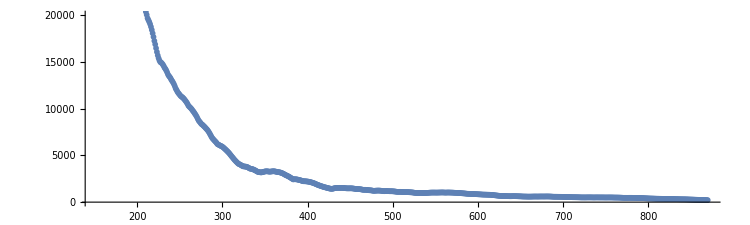

```mathematica
ListPlot[Transpose[{houseSizes, disenfranchisement}], ImageSize->750, AspectRatio->0.3]
```

Weighting the disparity between per-representative figures gives us a more sensible decline in the level of disenfranchisement as the size of the House increases. It doesn’t fix the algorithm, but it gives us a reliable way to meter future progress.